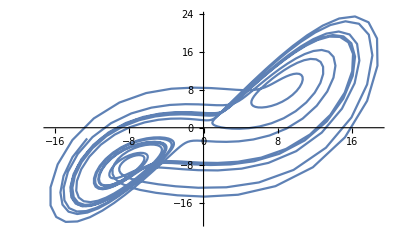

```mathematica
(* Lorenz attractor by simple Eulerian iteration.*)
s =10.0; b=8/3.0; r = 28.0;
dt = 0.02;
x = 0; y = 3;
z = 0;
attractor={};
Do[
vx =s(y-x);
vy=r x - y -x z;
vz = x y - b z;
x+= vx*dt;
y+= vy*dt;
z+= vz*dt;
If[q>100, attractor = Append[attractor,{x,y}]],{q,1,800}]
ListPlot[attractor, Joined->True, Ticks->None]
```